# GPU 执行与 CPU 对照

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## 模型、输入与适用范围

Same-input double-precision numerical comparison

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

运行小型 GPU/CPU 对照，保存工具链和数值误差。

## 推导与结果解释

在 CPU 与 GPU 上执行相同的小型双精度运算：矩阵乘法、已知解复线性系统及真实残差、FFT 与逆变换回读。

对照验收当前输入的算术和运行时一致性；新物理场解、大规模收敛和其他负载性能须分别验证。

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## 可编辑参数

```mathematica
parameters=<|"matrix_size"->128,"fft_size"->4096|>;parameters
```

<|matrix_size -> 128, fft_size -> 4096|>

## 独立进程执行与结果

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"gpu",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_gpu_20261014010725_a7e9c088, source_model -> gpu, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

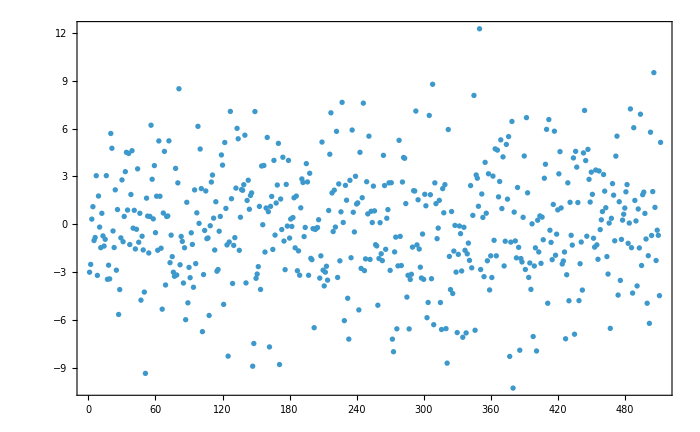

```mathematica
LitzNotebook`DisplayResearch[research]
```

## 验收与接续

核对结果中的 checks、execution_status 和 physical_acceptance_status。完整收敛与结构研究按路线 README 继续。

Sources: CUDA; references/library.bib and references/sources.json

## 历史证据

data/evidence/v1.0.0-rc.1/; litz-research data fetch gpu